### Zadanie 1

Użyj funkcji Plot do narysowania f(x) = Sin(1/x) w przedziale (0.01,1).

### Zadanie 2

Narysuj wykres funkcji f(x,y)=Cos(√(x^2+y^2)) w wybranym obszarze. Poeksperymentuj z opcjami PlotPoints aby otrzymac ladny wykres.

### Zadanie3

Dane sš funkcje f(x)=2 x^3-6x+3 i  g(x)=-4 x^3+3 x^2+2 .
(a)  Używajac graficznych funkcji narysuj obie funkcje na jednym wykresie i oszacuj punkty przecięcia się funkcji.
(b)  Znajd.9f punkty przecięcia się dwóch krzywych symbolicznie.
(c)  Znajd.9f punkty przecięcia się dwóch krzywych numerycznie .

### Zadanie 4

Dana jest funkcja f(x)=(x^3+x+1)/(x^4+1).
(a)  Znajd.9f wzoryf'(x) i f''(x) symbolicznie
(b) Znajd.9f miejsca zerowe funkcji f'(x) i f''(x). Jak wiadomo z analizy, sš to możliwe ekstrema funkcji f(x)
(c)  Narysuj wykresy f(x), f'(x) i f''(x) na jednym wykresie różnymi kolorami. Zinterpretuj rysunek- które punkty odnalezione w (b) sš eksterami, a które punktami przegięcia ?

zadanie

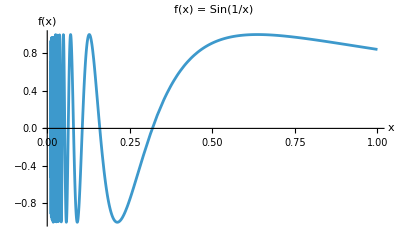

```mathematica
zadanie 1
Plot[Sin[1/x],{x,0.01,1},PlotLabel->"f(x) = Sin(1/x)",AxesLabel->{"x","f(x)"}]
```

```mathematica
zadanie 2
Plot3D[Cos[Sqrt[x^2+y^2]],{x,-15,15},{y,-15,15},PlotPoints->100,ColorFunction->"TemperatureMap",PlotLabel->"f(x,y) = Cos(Sqrt[x^2+y^2])"]
```

2 zadanie

-Graphics3D-

3 a zadanie

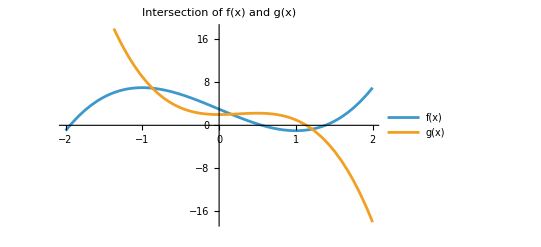

```mathematica
zadanie 3a
f[x_]:=2x^3-6x+3
g[x_]:=-4x^3+3x^2+2

Plot[{f[x],g[x]},{x,-2,2},PlotLegends->{"f(x)","g(x)"},PlotLabel->"Intersection of f(x) and g(x)"]
```

```mathematica
zadanie 3b
symbolicRoots=Solve[f[x]==g[x],x]
```

3 b zadanie

{{x→},{x→},{x→}}

```mathematica
zadanie 3c
numericRoots=NSolve[f[x]==g[x],x,Reals]
```

3 c zadanie

```mathematica
{{x->-0.8698662171283816},{x->0.15811908166098285},{x->1.2117471354673988}}
```

```mathematica
zadanie 4a
h[x_]:=(x^3+x+1)/(x^4+1)

firstDeriv=Simplify[D[h[x],x]]
secondDeriv=Simplify[D[h[x],{x,2}]]
```

4 a zadanie

-(-1-3 x^2+4 x^3+3 x^4+x^6)/((1+x^4)^2)

(2 x (3-6 x-10 x^2-12 x^4+10 x^5+6 x^6+x^8))/((1+x^4)^3)

```mathematica
zadanie 4b
extremaPoints=NSolve[firstDeriv==0,x,Reals]
inflectionPoints=NSolve[secondDeriv==0,x,Reals]
```

4 b zadanie

{{x→-1.36072},{x→0.734904}}

{{x→-1.84921},{x→-0.644103},{x→0.},{x→0.317765},{x→1.16285}}

4 c zadanie

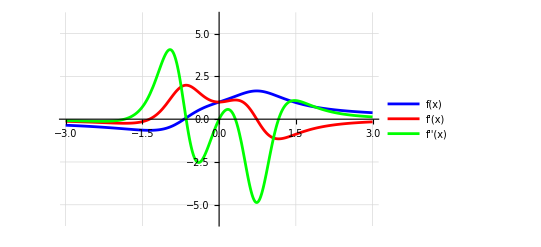

```mathematica
zadanie 4c
Plot[{h[x],firstDeriv,secondDeriv},{x,-3,3},PlotLegends->{"f(x)","f'(x)","f''(x)"},PlotStyle->{Blue,Red,Green},PlotRange->{-6,6},GridLines->Automatic]
```